# Dynamics of interacting particles

#### Abhishek Sharma BioMIP Ruhr Universität, Bochum, Germany

The interactions which arise from two dimensional particles can be assumed as superpostion of interaction from individual electrode . In the simplest form, assuming each electrode as a point, interaction from each electrode can be approximated by Yukawa type potential. The potential is monotone increasing, implying that force is always attractive (Currently, I don’t know the correct parameters to desribe the physically realistic interaction). Mathematically, this potential is given by :

                                                                      V_Yukawa(r) = -g^2 e^(-k  r)/r 
                                                                                  
where, g and k are scaling constants. So, we can define the Yukawa Potential as :

```mathematica
ClearAll["Global`*"]
```

```mathematica
VYukawa[{p_,q_},r_]:= -p^2 ⅇ^(-q r)/r
```

```mathematica
p1=Plot[Evaluate@Table[VYukawa[{1,q},r],{q,1,20,4}],{r,0,1}, PlotLabel-> "Yukawa Potential v/s distance", FrameLabel-> {"r","Potential"},BaseStyle->{FontWeight->"Bold",FontSize->10}, Frame-> True,PlotLegends->Placed[{"k=1","k=5","k=9","k=13","k=17"},{Right,Bottom}]];
```

```mathematica
p2=Plot[Evaluate[Table[VYukawa[{g,1},r],{g,1,20,4}]],{r,0,1},PlotLegends->Placed[{"g=1","g=5","g=9","g=13","g=17"},{Right, Bottom}], PlotLabel-> "Yukawa Potential v/s distance", FrameLabel-> {"r","Potential"},BaseStyle->{FontWeight->"Bold",FontSize->10}, Frame-> True];
```

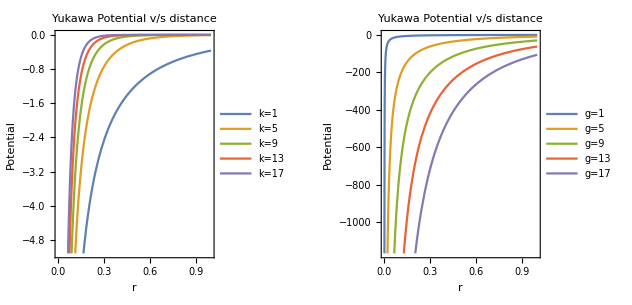

```mathematica
GraphicsRow[{p1,p2}]
```

### Extension to higher dimensions for particles and interacting surface

It is easy to extend these dimensions to higher dimensions. We extend this formulation to finite number of patterns on docking station (upto 9 docklets) and for single lablets to study their dynamics.

#### Case 1 : Creation of docking station surface potential

Suppose there exists two particles, which interact with each other via Yukawa Potential. The pair interaction force can be calculated by the gradient of the interaction potential. The pair interaction force in two dimensions is given by :

```mathematica
Grad[VYukawa[{p,q},√(x^2+y^2)],{x,y}]
```

{(ⅇ^(-q √(x^2+y^2)) p^2 x)/((x^2+y^2)^(3/2))+(ⅇ^(-q √(x^2+y^2)) p^2 q x)/(x^2+y^2),(ⅇ^(-q √(x^2+y^2)) p^2 y)/((x^2+y^2)^(3/2))+(ⅇ^(-q √(x^2+y^2)) p^2 q y)/(x^2+y^2)}

In normalized system, the interaction force between two particles at (x_1, y_1) and (x_2, y_2) is given by :

```mathematica
F1=FullSimplify[Grad[VYukawa[{p,q},√((x2-x1)^2+(y2 -y1)^2)],{x1,y1}]]
```

{(ⅇ^(-q √((x1-x2)^2+(y1-y2)^2)) p^2 (x1-x2) (1+q √((x1-x2)^2+(y1-y2)^2)))/(((x1-x2)^2+(y1-y2)^2)^(3/2)),(ⅇ^(-q √((x1-x2)^2+(y1-y2)^2)) p^2 (1+q √((x1-x2)^2+(y1-y2)^2)) (y1-y2))/(((x1-x2)^2+(y1-y2)^2)^(3/2))}

```mathematica
F2=FullSimplify[Grad[VYukawa[{p,q},√((x2-x1)^2+(y2 -y1)^2)],{x2,y2}]]
```

{-(ⅇ^(-q √((x1-x2)^2+(y1-y2)^2)) p^2 (x1-x2) (1+q √((x1-x2)^2+(y1-y2)^2)))/(((x1-x2)^2+(y1-y2)^2)^(3/2)),-(ⅇ^(-q √((x1-x2)^2+(y1-y2)^2)) p^2 (1+q √((x1-x2)^2+(y1-y2)^2)) (y1-y2))/(((x1-x2)^2+(y1-y2)^2)^(3/2))}

```mathematica
F1==-F2
```

True

```mathematica
Curl[F1,{x,y}]
```

0

As, F_1= -F_2 and Curl of the force is zero, this shows that the force is conservative.

Keeping the simple case in two dimensions, we define Lablet as a combination of eight electrodes. In two dimensional coodinate system, the position of  the centre of each electrode is given by (in terms of scaled units): 

{e1, e2, e3, e4, e5 ,e6, e7, e8} =  {{-1, -1}, {0, -1}, {1, -1}, {-1, 0}, {1, 0}, {-1, 1}, {0, 1}, {1, 1}}

```mathematica
e1 = {-1,-1};e2 = {0,-1};e3 = {1,-1};e4 = {-1,0};e5 = {1,0};e6 = {-1,1};e7 = {0,1};e8 = {1,1};
```

```mathematica
pos=Transpose[{e1, e2, e3, e4, e5, e6, e7, e8}]
```

{{-1,0,1,-1,1,-1,0,1},{-1,-1,-1,0,0,1,1,1}}

```mathematica
posAll=Flatten[Table[Table[{i,j},{8}]+MapThread[{#1,#2}&,pos],{i,-3,3,3},{j,-3,3,3}],2];
```

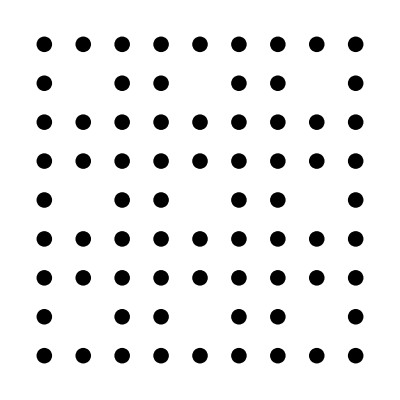

```mathematica
Graphics[Disk[#,0.2]&/@posAll]
```

In two dimensional coordinate system, we define the Yukawa Potential as :

```mathematica
VYukawa[{p_,q_},{x_,y_,z_},{x1_,y1_}]:= -p^2(ⅇ^(-q √((x-x1)^2+(y-y1)^2+z^2)))/(√((x-x1)^2+(y-y1)^2+z^2))
```

```mathematica
Plot3D[VYukawa[{1,0},{x,y,0},{0.,0.}],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Pot[{p_,q_},{x_,y_,z_}]=Total[MapThread[VYukawa[{p,q},{x,y,z},{#1,#2}]&,pos]]
```

-(ⅇ^(-q √((-1+x)^2+(-1+y)^2+z^2)) p^2)/(√((-1+x)^2+(-1+y)^2+z^2))-(ⅇ^(-q √(x^2+(-1+y)^2+z^2)) p^2)/(√(x^2+(-1+y)^2+z^2))-(ⅇ^(-q √((1+x)^2+(-1+y)^2+z^2)) p^2)/(√((1+x)^2+(-1+y)^2+z^2))-(ⅇ^(-q √((-1+x)^2+y^2+z^2)) p^2)/(√((-1+x)^2+y^2+z^2))-(ⅇ^(-q √((1+x)^2+y^2+z^2)) p^2)/(√((1+x)^2+y^2+z^2))-(ⅇ^(-q √((-1+x)^2+(1+y)^2+z^2)) p^2)/(√((-1+x)^2+(1+y)^2+z^2))-(ⅇ^(-q √(x^2+(1+y)^2+z^2)) p^2)/(√(x^2+(1+y)^2+z^2))-(ⅇ^(-q √((1+x)^2+(1+y)^2+z^2)) p^2)/(√((1+x)^2+(1+y)^2+z^2))

```mathematica
Plot3D[Pot[{2,2},{x,y,0}],{x,-3,3},{y,-3,3},MaxRecursion->3]
```

-Graphics3D-

So, this could be easily extended to multiple copies, to create a region of docking station :

```mathematica
Pot[{p_,q_},{x_,y_,z_}]=Total[MapThread[VYukawa[{p,q},{x,y,z},{#1,#2}]&,Transpose[posAll]]];
```

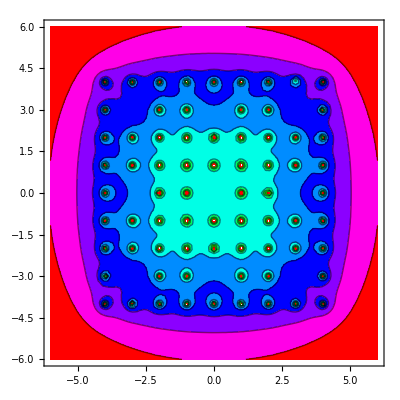

```mathematica
ContourPlot[Pot[{1,0},{x,y,0}],{x,-6,6},{y,-6,6},MaxRecursion-> 2,Contours-> 8,ColorFunction->Hue]
```

#### Equipotential surface around a particle in three dimensional space

Consider a free moving particle at a position (X, Y, Z) and orientation (θ, ϕ, ψ) with respect the three axes passing through the centre of the lablet. To get coordinates of all electrodes general direction defined by orientation angles (θ, ϕ, ψ), we first rotate the lablet containing electrodes at the origin, and translate it to the correct position.

The generalized rotation matrix along three axis is given by,

```mathematica
rotMat[θ_,ϕ_,ψ_] :=RotationMatrix[θ,{1,0,0}].RotationMatrix[ϕ,{0,1,0}].RotationMatrix[ψ,{0,0,1}]
```

```mathematica
rotMat[θ,ϕ,ψ]//MatrixForm
```

(Cos[ϕ] Cos[ψ] | -Cos[ϕ] Sin[ψ] | Sin[ϕ]
Cos[ψ] Sin[θ] Sin[ϕ]+Cos[θ] Sin[ψ] | Cos[θ] Cos[ψ]-Sin[θ] Sin[ϕ] Sin[ψ] | -Cos[ϕ] Sin[θ]
-Cos[θ] Cos[ψ] Sin[ϕ]+Sin[θ] Sin[ψ] | Cos[ψ] Sin[θ]+Cos[θ] Sin[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ])

The position of all the electrodes of the particle are given by,

```mathematica
e1 = {-1,-1,0};e2 = {0,-1,0};e3 = {1,-1,0};e4 = {-1,0,0};e5 = {1,0,0};e6 = {-1,1,0};e7 = {0,1,0};e8 = {1,1,0};
```

```mathematica
electrodes = {e1,e2,e3,e4,e5,e6,e7,e8};
```

So, rotating each electrode of the lablet

```mathematica
rotElectrodes[{θ_,ϕ_,ψ_}]:=(rotMat[θ,ϕ,ψ].#)&/@ electrodes
```

```mathematica
posElectrodes[{x_,y_,z_},{θ_,ϕ_,ψ_}]:=(#+{x,y,z})&/@rotElectrodes[{θ,ϕ,ψ}]
```

So, with this generalize function for particles, we can rotate the electrodes accordingly.

We can create generalized force field using Yukawa potential, for a particle as function of position and rotation.

```mathematica
VYukawa3D[{p_,q_},{x_,y_,z_},{x1_,y1_,z1_}]:= -p^2(ⅇ^(-q √((x-x1)^2+(y-y1)^2+(z-z1)^2)))/(√((x-x1)^2+(y-y1)^2+(z-z1)^2))
```

And, generalized expression for the Lablet potential and force in three dimensions is given by :

```mathematica
VYukawa3D[{p_,q_},{x_,y_,z_},{x1_,y1_,z1_},{θ_,ϕ_,ψ_}]:=Total[MapThread[VYukawa3D[{p,q},{x,y,z},{#1,#2,#3}]&,Transpose[posElectrodes[{x1,y1,z1},{θ,ϕ,ψ}]]]]
```

```mathematica
Field3D[{p_,q_},{x_,y_,z_},{x1_,y1_,z1_},{θ_,ϕ_,ψ_}]= Grad[VYukawa3D[{p,q},{x,y,z},{x1,y1,z1},{θ,ϕ,ψ}], {x,y,z}];
```

```mathematica
{Curl[Field3D[{p,q},{x2,y2,z2},{x1,y1,z1},{θ,ϕ,ψ}],{x1,y1,z1}],Curl[Field3D[{p,q},{x2,y2,z2},{x1,y1,z1},{θ,ϕ,ψ}],{x2,y2,z2}]}
```

{{0,0,0},{0,0,0}}

So, we can see equipotential surfaces around the Lablet :

```mathematica
ContourPlot3D[Evaluate[VYukawa3D[{3,3},{x,y,z},{0.,0.,0.},π/180{15.,15.,15.}]],{x,-3,3},{y,-3,3},{z,-3,3}, Mesh-> None, Contours-> 3,MaxRecursion->2,ContourStyle->Directive[Orange,Opacity[0.3],Specularity[White,30]], PlotLabel-> "Equipotential surface around a Lablet",BaseStyle->{FontWeight->"Bold",FontSize->10}]
```

-Graphics3D-

#### Pairwise interaction force between two Lablets

Consider two Lablets with their COG at position vectors (X_1, Y_1, Z_1) and (X_2, Y_2, Z_2), and respective orientations given by (θ_1, ϕ_1, ψ_1) and (θ_2, ϕ_2, ψ_2). 
As the force between two particles acts only along the line joining their center of masses, the total force can be written as the summation of forces from individual electrodes.

```mathematica
pairForce[{p_,q_},{x1_,y1_,z1_},{θ1_,ϕ1_,ψ1_},{x2_,y2_,z2_},{θ2_,ϕ2_,ψ2_}]=Total[MapThread[Field3D[{p,q},{#1,#2,#3},{x1,y1,z1},{θ1,ϕ1,ψ1}]&,Transpose[ posElectrodes[{x2,y2,z2},{θ2,ϕ2,ψ2}]]]];
```

```mathematica
{Curl[pairForce[{p,q},{x1,y1,z1},{θ1,ϕ1,ψ1},{x2,y2,z2},{θ2,ϕ2,ψ2}],{x1, y1, z1}],Curl[pairForce[{p,q},{x1,y1,z1},{θ1,ϕ1,ψ1},{x2,y2,z2},{θ2,ϕ2,ψ2}],{x2, y2, z2}]}
```

{{0,0,0},{0,0,0}}

As the mathematical expressions becomes too long, we can check the forces by putting position and orientation vectors, as an example putting arbitirary values of positional and orientational vectors

```mathematica
F1=pairForce[{1.,1.},{1.,2.,3.},{4.,5.,6.},{6.,5.,4.},{3.,2.,1.}];
F2=pairForce[{1.,1.},{6.,5.,4.},{3.,2.,1.},{1.,2.,3.},{4.,5.,6.}];
```

```mathematica
F1== -F2
```

True

```mathematica
F1
```

{0.0323819,0.0140289,0.00743171}

To calculate torque between two Lablets, we consider two particles with position and orientational vectors as  (X_1, Y_1, Z_1,θ_1, ϕ_1, ψ_1) and (X_2, Y_2, Z_2,θ_2, ϕ_2, ψ_2). We measure the torque on the particles at the centre of gravity.

So, with respect to COG of the particles, the position vector of electrodes are given by :

For some reasons, Mathematica inbulit function Cross takes too much of time while evalulation so I define myself crossproduct function as :

```mathematica
crossproduct[{x1_,y1_,z1_},{x2_,y2_,z2_}]:={-y2 z1+y1 z2,x1 z1-x1 z2,-x1 y1+x1 y2}
```

```mathematica
pairTorque[{p_,q_},{x1_,y1_,z1_},{θ1_,ϕ1_,ψ1_},{x2_,y2_,z2_},{θ2_,ϕ2_,ψ2_}]=Total[MapThread[crossproduct[{#1,#2,#3},Field3D[{p,q},{#1,#2,#3},{x1,y1,z1},{θ1,ϕ1,ψ1}]]&,Transpose[posElectrodes[{x2,y2,z2},{θ2,ϕ2,ψ2}]]]];
```

As an example,

```mathematica
pairTorque[{1.,1.},{0.,0.,0.},{0.,0.,90 π/180},{5.,0.,0.},{0.,0.,90 π/180}]
```

{0.,0.,-6.93889×10^-18}

Based on these type of interactions, we can minimize the energy of the particles to calculate equilibriated self-assembled structures.

In this Mathematica file, we will consider various types of interactions that could be useful for self - assembly of particles. We will compare the order of interaction potential energies and corresponding forces, that could be useful particle - particle interactions at small and large length scales. Basically, there are always some interactions that could not be avoided for example gravitational forces, drag force etc. Usually, we have to compete with these interactions to find interactions for self - assenmbly. In this file, we will first calculate each type of interaction and give a comparitive study.

### Interactions between moving Lablets

#### Understanding dynamics of Lablets in Yukawa type field

```mathematica
VYukawa[{p_,q_},r_]:= p^2 ⅇ^(-q r)/r
```

```mathematica
sol=NDSolve[{D[x[t],{t,2}]== (D[VYukawa[{1,1},x],x]/.x-> x[t]),x'[0]== 0,x[0]== 5},x[t],{t,0,45}]
```

{{x[t]→InterpolatingFunction[{{0., 45.}}, <>][t]}}

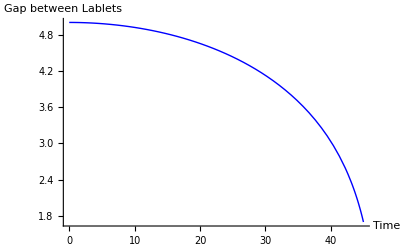

```mathematica
Plot[x[t]/.sol,{t,0,45},PlotStyle-> {Thick,Blue},AxesLabel->{"Time","Gap between Lablets"}]
```

#### Extension to two dimensions

In this subsection, we extend dynamics of particles in Yukawa field to two dimensions. We consider two dimensional analogue of docking station, which includes one dimensional array of electrodes, whole interaction potential is defined by Yukawa type potential given by : 

                                                                          V_Yukawa= p^2/(^(√((x-x_0)^2+(y-y_0)^2)))e^(-q √((x-x_0)^2+(y-y_0)^2))
                                                                          
                 where, {x_0,y_0} defines the position of the electrode on docking station, {x,y} describes the position of the electrode on the Lablet.                                                         For a simple calculation, inititally, we consider Lablet as a single electrode, hence we define the potential from docking station as :

```mathematica
VYukawa[{p_,q_,n_},{x_,y_},{x0_,y0_}]:= (-1)^n p^2(ⅇ^(-q √((x-x0)^2+(y-y0)^2)))/(√((x-x0)^2+(y-y0)^2))
```

We define periodic dimensionaless position of docking electrodes :

```mathematica
nE=10; (* Number of electrodes *)
```

```mathematica
positions={#,0}&/@Range[-nE/2,nE/2]
```

{{-5,0},{-4,0},{-3,0},{-2,0},{-1,0},{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}}

```mathematica
nType={0,1,0,1,0,1,0,1,0,1,0};
```

```mathematica
VYukawaTot[x_,y_]=Total@MapThread[VYukawa[{1,1,#1},{x,y},#2]&,{nType,positions}]
```

(ⅇ^(-√((-5+x)^2+y^2)))/(√((-5+x)^2+y^2))-(ⅇ^(-√((-4+x)^2+y^2)))/(√((-4+x)^2+y^2))+(ⅇ^(-√((-3+x)^2+y^2)))/(√((-3+x)^2+y^2))-(ⅇ^(-√((-2+x)^2+y^2)))/(√((-2+x)^2+y^2))+(ⅇ^(-√((-1+x)^2+y^2)))/(√((-1+x)^2+y^2))-(ⅇ^(-√(x^2+y^2)))/(√(x^2+y^2))+(ⅇ^(-√((1+x)^2+y^2)))/(√((1+x)^2+y^2))-(ⅇ^(-√((2+x)^2+y^2)))/(√((2+x)^2+y^2))+(ⅇ^(-√((3+x)^2+y^2)))/(√((3+x)^2+y^2))-(ⅇ^(-√((4+x)^2+y^2)))/(√((4+x)^2+y^2))+(ⅇ^(-√((5+x)^2+y^2)))/(√((5+x)^2+y^2))

```mathematica
ContourPlot[VYukawaTot[x,y],{x,-4,4},{y,0,2},MaxRecursion-> 5]
```

-Graphics-

Force on a single electrode type Lablet is given by gradient of potential, which is equal to

```mathematica
ForceLablet[x_,y_]=Grad[VYukawaTot[x,y],{x,y}];
```

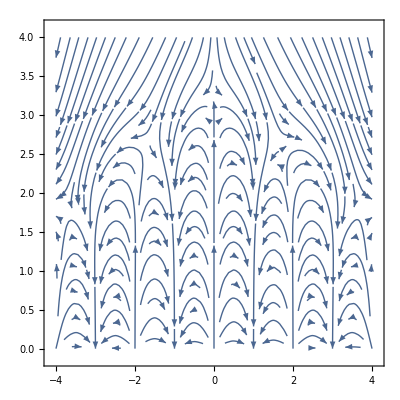

```mathematica
StreamPlot[ForceLablet[x,y],{x,-4,4},{y,0,4},StreamScale-> Large,StreamPoints-> Fine]
```

```mathematica
{Fx,Fy}=ForceLablet[x,y];
```

```mathematica
eqns={(Fx/.{x-> x[t],y-> y[t]})== D[x[t],{t,2}],(Fy/.{x-> x[t],y-> y[t]})== D[y[t],{t,2}],x'[0]== 0,y'[0]== 0,x[0]== -4,y[0]== 0.5};
```

```mathematica
sol=NDSolve[eqns,{x[t],y[t]},{t,0,10}]
```

{{x[t]→InterpolatingFunction[{{0., 10.}}, <>][t],y[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

```mathematica
ParametricPlot[{x[t],y[t]}/.sol,{t,0,10},PlotStyle-> {Blue,Thick}];
```

### Interactions between two Lablets

#### Case 1 : Each Lablet is defined by a single electrode

Two dimensional formulation of Yukawa potential is given by :

```mathematica
VYukawa[{p_,q_,n_},{x_,y_},{x0_,y0_}]:= (-1)^n p^2(ⅇ^(-q √((x-x0)^2+(y-y0)^2)))/(√((x-x0)^2+(y-y0)^2))
```

As, each Lablet is defined as a single electrode, we consider Lablet as a point particle, hence the interaction force between two such point particles in two dimensions is given by :

```mathematica
PairIntForce[{p_,q_,n_},{x1_,y1_},{x2_,y2_}]=Grad[VYukawa[{p,q,n},{x1,y1},{x2,y2}],{x1,y1}]
```

{((-1)^(1+n) ⅇ^(-q √((x1-x2)^2+(y1-y2)^2)) p^2 (x1-x2))/(((x1-x2)^2+(y1-y2)^2)^(3/2))+((-1)^(1+n) ⅇ^(-q √((x1-x2)^2+(y1-y2)^2)) p^2 q (x1-x2))/((x1-x2)^2+(y1-y2)^2),((-1)^(1+n) ⅇ^(-q √((x1-x2)^2+(y1-y2)^2)) p^2 (y1-y2))/(((x1-x2)^2+(y1-y2)^2)^(3/2))+((-1)^(1+n) ⅇ^(-q √((x1-x2)^2+(y1-y2)^2)) p^2 q (y1-y2))/((x1-x2)^2+(y1-y2)^2)}

```mathematica
FullSimplify[PairIntForce[{p,q,n},{x1,y1},{x2,y2}]]== -FullSimplify[PairIntForce[{p,q,n},{x2,y2},{x1,y1}]]
```

True

```mathematica
rules={x1-> x1[t],x2-> x2[t],y1-> y1[t],y2-> y2[t]};
```

```mathematica
{Fxp1,Fyp1}=FullSimplify[PairIntForce[{p,q,n},{x1,y1},{x2,y2}]]/.rules;
```

```mathematica
{Fxp2,Fyp2}=FullSimplify[PairIntForce[{p,q,n},{x2,y2},{x1,y1}]]/.rules;
```

Hence, using this pair interaction force, we can formulate the equations of motion for the two particles as  :

```mathematica
govEquations[{m1_,m2_},{p_,q_,n_}]={Fxp1== m1 x1''[t],Fyp1== m1 y1''[t],Fxp2== m1 x2''[t],Fyp2== m2 y2''[t]};
```

```mathematica
initVelocities={x1'[0]== 0.1,y1'[0]== 0,x2'[0]==0,y2'[0]== 0};
```

```mathematica
initPositions={x1[0]== 1,y1[0]== 1,x2[0]== 5,y2[0]== 6};
```

```mathematica
initConditions={initVelocities,initPositions}//Flatten;
```

```mathematica
totalEquations[{m1_,m2_},{p_,q_,n_}]={govEquations[{m1,m2},{p,q,n}],initConditions}//Flatten;
```

```mathematica
sol=NDSolve[totalEquations[{1,1},{5,1,0}],{x1[t],y1[t],x2[t],y2[t]},{t,0,200}]
```

{{x1[t]→InterpolatingFunction[{{0., 200.}}, <>][t],y1[t]→InterpolatingFunction[{{0., 200.}}, <>][t],x2[t]→InterpolatingFunction[{{0., 200.}}, <>][t],y2[t]→InterpolatingFunction[{{0., 200.}}, <>][t]}}

```mathematica
({x1[t],y1[t]}/.sol)
```

{{InterpolatingFunction[{{0., 200.}}, <>][t],InterpolatingFunction[{{0., 200.}}, <>][t]}}

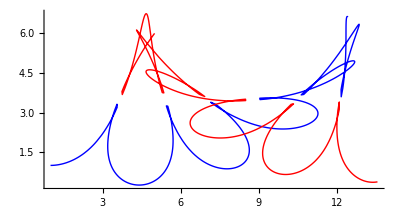

```mathematica
Show[ParametricPlot[({x1[t],y1[t]}/.sol),{t,0,200},PlotStyle-> {Blue, Thick}],ParametricPlot[({x2[t],y2[t]}/.sol),{t,0,200},PlotStyle-> {Red, Thick}],PlotRange-> All]
```

#### Case 2 : Each Lablet is defined by combination of electrodes : Pure Translational Motion

Here, we define the two dimensional analogue of a Lablets, with four electrode at the corners, whose interactions are described by Yukawa potential. Lablet is defined as a unit square, whose positions of electrodes wrt. center of Lablet are given by :

```mathematica
Clear[positions]
```

```mathematica
VYukawa[{p_,q_,n_},{x_,y_},{x0_,y0_}]:= (-1)^n p^2(ⅇ^(-q √((x-x0)^2+(y-y0)^2)))/(√((x-x0)^2+(y-y0)^2))
```

```mathematica
positions[x_,y_]:={{-1/2+x, -1/2+y},{-1/2+x,1/2+y},{1/2+x,-1/2+y},{1/2+x,1/2+y}};
```

```mathematica
genPositions[x_,y_,θ_]:={x,y}+#&/@(RotationMatrix[θ].#&/@{{-1/2,-1/2},{-1/2,1/2},{1/2,1/2},{1/2,-1/2}})
```

```mathematica
nType={1,1,1,1};
```

```mathematica
VYukawaTot[{x_,y_},{x0_,y0_,θ0_}]= Total@(MapThread[VYukawa[{1,1,#1},{x,y},#2]&,{nType,genPositions[x0,y0,θ0]}]);
```

```mathematica
Plot3D[VYukawaTot[{x,y},{0,0,0}],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

Now, we consider two different Lablets, in different orientations at whose positions and angles (wrt. X axis) are given by : 
P_1={x_1,y_1,θ_1}, P_2={x_2,y_2,θ_2}. Suppose initital positions of Lablets are : {{-1,-1}, {6,5}}

```mathematica
FieldLablet[{x_,y_},{x0_,y0_,θ0_}]=Grad[VYukawaTot[{x,y},{x0,y0,θ0}],{x,y}];
```

```mathematica
pairForce[{x1_,y1_,θ1_},{x2_,y2_,θ2_}]=Total@(FieldLablet[#,{x1,y1,θ1}]&/@genPositions[x2,y2,θ2]);
```

```mathematica
{pairForce[{-1,-1,(3π)/4},{5,6,(2π)/3}],pairForce[{5,6,(2π)/3},{-1,-1,(3π)/4}]}//N
```

{{0.000162891,0.00018942},{-0.000162891,-0.00018942}}

```mathematica
{Curl[pairForce[{x1,y1,θ1},{x2,y2,θ2}],{x1,y1}],Curl[pairForce[{x1,y1,θ1},{x2,y2,θ2}],{x2,y2}]}
```

{0,0}

Based on the pair interaction force, we can write the governing equations of motion as we did in the last section.

```mathematica
rules={x1-> x1[t],x2-> x2[t],y1-> y1[t],y2-> y2[t]};
```

```mathematica
θfixedRules={θ1-> 0,θ2-> 0};
```

```mathematica
{Fxp1,Fyp1}=pairForce[{x1,y1,θ1},{x2,y2,θ2}]/.rules/.θfixedRules;
```

```mathematica
{Fxp2,Fyp2}=pairForce[{x2,y2,θ2},{x1,y1,θ1}]/.rules/.θfixedRules;
```

Hence, using this pair interaction force, we can formulate the equations of motion for the two particles as  :

```mathematica
govEquations[{m1_,m2_},{p_,q_,n_}]={Fxp1== m1 x1''[t],Fyp1== m1 y1''[t],Fxp2== m1 x2''[t],Fyp2== m2 y2''[t]};
```

```mathematica
initVelocities={x1'[0]== 0.1,y1'[0]== 0,x2'[0]==0,y2'[0]== 0};
```

```mathematica
initPositions={x1[0]== 1,y1[0]== 1,x2[0]== 5,y2[0]== 6};
```

```mathematica
initConditions={initVelocities,initPositions}//Flatten;
```

```mathematica
totalEquations[{m1_,m2_}]={govEquations[{m1,m2},{p,q,n}],initConditions}//Flatten;
```

```mathematica
totalEquations[{1,1}]//MatrixForm;
```

```mathematica
sol=NDSolve[totalEquations[{1,1}],{x1[t],y1[t],x2[t],y2[t]},{t,0,200}]
```

{{x1[t]→InterpolatingFunction[{{0., 200.}}, <>][t],y1[t]→InterpolatingFunction[{{0., 200.}}, <>][t],x2[t]→InterpolatingFunction[{{0., 200.}}, <>][t],y2[t]→InterpolatingFunction[{{0., 200.}}, <>][t]}}

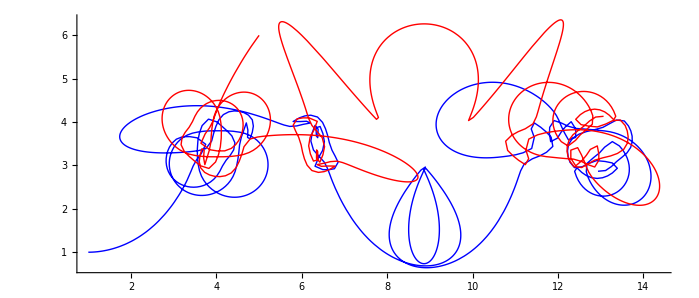

```mathematica
Show[ParametricPlot[({x1[t],y1[t]}/.sol),{t,0,200},PlotStyle-> {Blue, Thick}],ParametricPlot[({x2[t],y2[t]}/.sol),{t,0,200},PlotStyle-> {Red, Thick}],PlotRange-> All]
```

#### Case 2 : Coupled Rotational and Translational Motion

In case if coupled rotational and translational motion, we consider pair force interaction and pair torques between two particles. Pair force is defined in the last subsection, here we defined both pair force and pair torque, and then write down the equations of both rotational and translational motion.

```mathematica
VYukawaTot[{x_,y_},{x0_,y0_,θ0_}]= Total@(MapThread[VYukawa[{0.7,2,#1},{x,y},#2]&,{nType,genPositions[x0,y0,θ0]}]);
```

```mathematica
FieldLablet[{x_,y_},{x0_,y0_,θ0_}]=Grad[VYukawaTot[{x,y},{x0,y0,θ0}],{x,y}];
```

```mathematica
pairForce[{x1_,y1_,θ1_},{x2_,y2_,θ2_}]=Total@(FieldLablet[#,{x1,y1,θ1}]&/@genPositions[x2,y2,θ2]);
```

To calculate the pair torque, we calculate individual force on each of the electrode of the Lablet from the electrodes of all the other Lablet. Then, pair torque will be calculated taking cross product of position wrt. to COM of the Lablet. So, we define the cross product as :

```mathematica
crossProduct[{a1_,b1_},{a2_,b2_}]:= a1 b2 +a2 b1
```

```mathematica
torque[{x_,y_},{xc_,yc_},{x0_,y0_,θ0_}]:=crossProduct[{x-xc,y-yc},FieldLablet[{x,y},{x0,y0,θ0}]]
```

```mathematica
pairTorque[{x_,y_,θ_},{x0_,y0_,θ0_}]=Total@(torque[#,{x,y},{x0,y0,θ0}]&/@genPositions[x,y,θ]);
```

```mathematica
{pairTorque[{-1,-1,(3π)/4} ,{5,6,(2π)/3}],pairTorque[{5,6,(2π)/3},{-1,-1,(3π)/4}]}//N
```

{-1.83322×10^-8,-1.89929×10^-8}

#### Coupled governing rotational and translational equations of motion

Governing rotational and translational equations of motion are given by :

```mathematica
rules={x1->x1[t],x2->x2[t],y1->y1[t],y2->y2[t],θ1->θ1[t],θ2->θ2[t]};
```

```mathematica
pairForce[{x1_,y1_,θ1_},{x2_,y2_,θ2_}]=Total@(FieldLablet[#,{x1,y1,θ1}]&/@genPositions[x2,y2,θ2]);
```

```mathematica
{Fxp1,Fyp1}=pairForce[{x1,y1,θ1},{x2,y2,θ2}]/.rules;
```

```mathematica
{Fxp2,Fyp2}=pairForce[{x2,y2,θ2},{x1,y1,θ1}]/.rules;
```

```mathematica
τp1=pairTorque[{x1,y1,θ1},{x2,y2,θ2}]/.rules;
```

```mathematica
τp2=pairTorque[{x2,y2,θ2},{x1,y1,θ1}]/.rules;
```

```mathematica
govEquations[{m1,m2},{I1,I2},{p,q,n}]={Fxp1== m1 x1''[t],Fyp1== m1 y1''[t],Fxp2== m1 x2''[t],Fyp2== m2 y2''[t],τp1==I1 θ1''[t],τp2==I2 θ2''[t]};
```

```mathematica
initVelocities={x1'[0]== 0.05,y1'[0]== 0,x2'[0]==0,y2'[0]== 0,θ1'[0]==0,θ2'[0]==0};
```

```mathematica
initPositions={x1[0]== 1,y1[0]== 1,x2[0]== 5,y2[0]== 6,θ1[0]==π/3,θ2[0]==π/4};
```

```mathematica
initConditions={initVelocities,initPositions}//Flatten;
```

```mathematica
totalEquations[{m1_,m2_},{I1_,I2_},{p_,q_,n_}]={govEquations[{m1,m2},{I1,I2},{p,q,n}],initConditions}//Flatten;
```

```mathematica
eqnsFinal=totalEquations[{1,1},{1,1},{0.1,10,1}]//Flatten;
```

```mathematica
sol=NDSolve[eqnsFinal,{x1[t],y1[t],x2[t],y2[t],θ1[t],θ2[t]},{t,0,1000}]
```

{{x1[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],y1[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],x2[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],y2[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],θ1[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],θ2[t]→InterpolatingFunction[{{0., 1000.}}, <>][t]}}

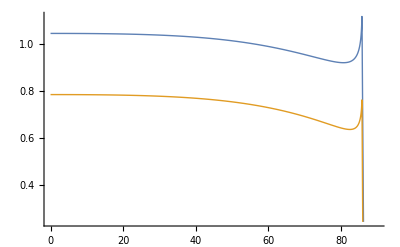

```mathematica
Plot[Evaluate[({θ1[t],θ2[t]}/.sol)],{t,0,90},PlotStyle-> Thick]
```

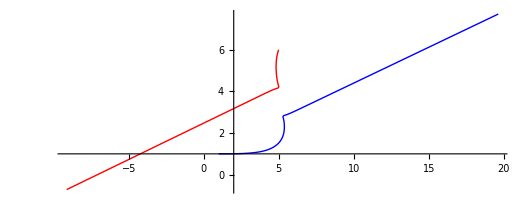

```mathematica
Show[ParametricPlot[({x1[t],y1[t]}/.sol),{t,0,90},PlotStyle-> {Blue, Thick}],ParametricPlot[({x2[t],y2[t]}/.sol),{t,0,90},PlotStyle-> {Red, Thick}],PlotRange-> All]
```

```mathematica
plotLablet2D[pts_]:={Yellow,Polygon[pts],Black,PointSize[0.01],Point[pts]};
```

```mathematica
plotLablets[{{x1_,y1_,θ1_},{x2_,y2_,θ2_}}]:=Block[{p1,p2},p1=genPositions[x1,y1,θ1];p2=genPositions[x2,y2,θ2];Graphics[{LightYellow,Polygon[{{-10,-10},{10,-10},{10,10},{-10,10}}],plotLablet2D[p1],plotLablet2D[p2]}]];
```

```mathematica
plotFunc[t_]=plotLablets[{{x1[t],y1[t],θ1[t]}/.sol//Flatten,{x2[t],y2[t],θ2[t]}/.sol//Flatten}];
```

```mathematica
Animate[plotFunc[t],{t,1,90},AnimationRunning-> False]
```